```mathematica
Clear[a,e]
V[a_,e_]:= 1/2*(1+Sqrt[1-e^2(1-a^2)]);
exp1 = (y - (1+a)(1+e)/4)*(V[a,e]-y-(1-a)(1-e)/4);
exp2 = (z-Sqrt[1-a^2]Sqrt[1-e^2]/4)^2;
exp3 = (y - (1-a)(1+e)/4)*(V[a,e]-y-(1+a)(1-e)/4);
exp4 = (z+Sqrt[1-a^2]Sqrt[1-e^2]/4)^2;
Solve[exp1 == exp2&&exp3==exp4,{y,z}]//FullSimplify
```

```mathematica
({{y->((1+e) (1+(-1+a^2) e+√(1+(-1+a^2) e^2)))/(4 √(1+(-1+a^2) e^2)), z->(a √(1-a^2) e √(1-e^2))/(4 √(1+(-1+(`a)^2) e^2))}, {y->((1+e) (1+(-1+a^2) e+√(1+(-1+a^2) e^2)))/(4 √(1+(-1+a^2) e^2)), z->(a √(1-a^2) e √(1-e^2))/(4 √(1+(-1+a^2) e^2))}})
```

```mathematica
Solve[0.0664761515876241-0.5 √(2.0782790245375424+16. (-0.7200000000000001+w) w)==0,w]
```

{{w→0.331499},{w→0.388501}}

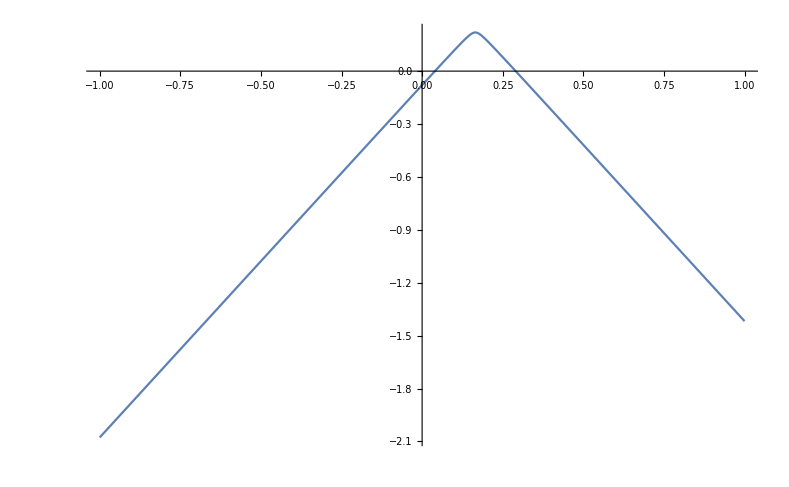

```mathematica
Plot[0.25265491900843107-0.5 √(0.44006005296762707+16. (-0.3299999999999999+w) w),{w,-1,1}]
```